On commence par ouvrir la boite à outil Mathematica pour faire des quadrature de Gauss-Legendre

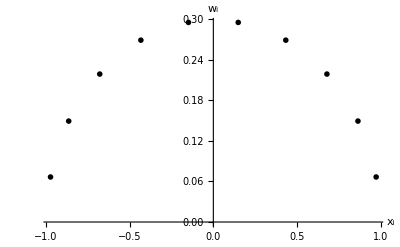

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
ListPlot[
GaussianQuadratureWeights[10,-1,1]
,AxesLabel->{"x_i","w_i"},PlotTheme->"Monochrome"]
```

```mathematica
(*
x/:Subscript[x, i_,n_]:=x/:Subscript[x, i,n]=Root[Function[x,LegendreP[n,x]],i]
w/:Subscript[w, i_,n_]:=w/:Subscript[w, i,n]=(2(1-Subscript[x, i,n]^2))/((n+1)^2 LegendreP[n+1,Subscript[x, i,n]]^2)//RootReduce
*)
```

## Projections pour une fonction en θ seulement, ou en x=cos(θ)

Soit un polynome d’ordre m:

```mathematica
Subscript[p, m_][x_]:=Sum[Subscript[a, j] x^j,{j,0,m}]   (* ceci est un polynome d'ordre m *)
```

Pour l’exemple, je me donne un polynome d’ordre 7

```mathematica
f[x_]:=Subscript[p, 7][x]
f[x] (* print f(x)  *)
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6+x^7 a_7

Je projete f(x) sur une base de polynomes de Legendre. Les N projections s’appellent f_0,f_1,...,f_N. Chaque f_m est définit par :

```mathematica
Subscript[f, m_]:=(2m+1)1/2 Integrate[   f[x]*LegendreP[m,x] ,{x,-1,1}  ]                  (* Note MMA: LegendreP[m,Cos@x]==WignerD[{m,0,0},x]   *)
```

Les 11 premiers polynomes de Legendre sont définis comme:

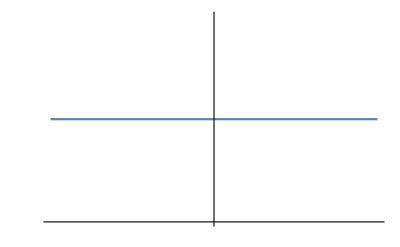
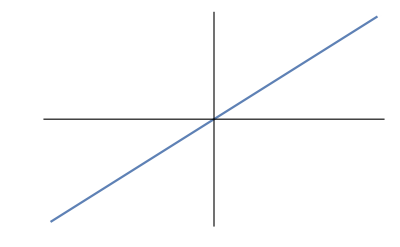
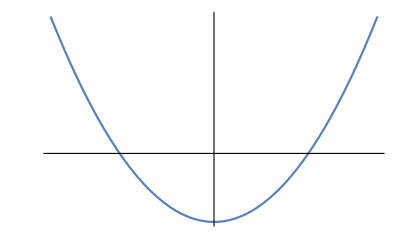
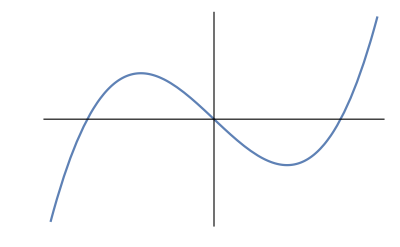
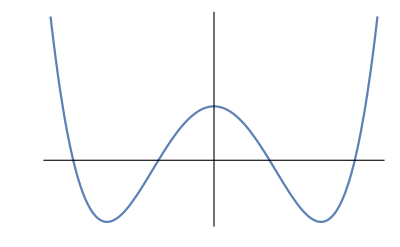
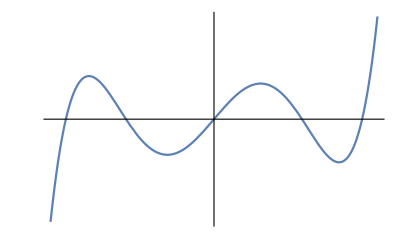
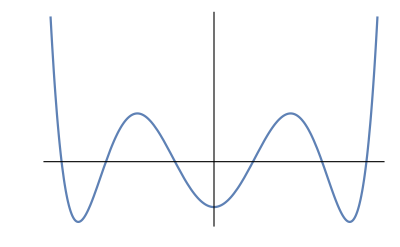
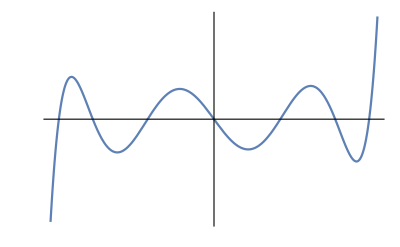
0 | 1 | -Graphics-
1 | x | -Graphics-
2 | 1/2 (-1+3 x^2) | -Graphics-
3 | 1/2 (-3 x+5 x^3) | -Graphics-
4 | 1/8 (3-30 x^2+35 x^4) | -Graphics-
5 | 1/8 (15 x-70 x^3+63 x^5) | -Graphics-
6 | 1/16 (-5+105 x^2-315 x^4+231 x^6) | -Graphics-
7 | 1/16 (-35 x+315 x^3-693 x^5+429 x^7) | -Graphics-
8 | 1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8) | -Graphics-
9 | 1/128 (315 x-4620 x^3+18018 x^5-25740 x^7+12155 x^9) | -Graphics-
10 | 1/256 (-63+3465 x^2-30030 x^4+90090 x^6-109395 x^8+46189 x^10) | -Graphics-

```mathematica
Table[
{
i,
LegendreP[i,x],
Plot[LegendreP[i,x],{x,-1,1}  ,PlotTheme->"Minimal"]
},{i,0,10}]//Grid
```

Je veux maintenant vérifier que je peux reformer f(x) depuis les N=7 premières projections

```mathematica
∑_(m=0)^7 Subscript[f, m] mx//Expand
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6+x^7 a_7

```mathematica
f[x]==Sum[
Subscript[f, m] LegendreP[m,x]
,{m,0,7}
]//Simplify
```

True

Avec 6 projections, ça ne fonctionne pas. Avec plus de 6 projections, ça fonctionne.
Il faut (n+1) projections pour faire l’aller-retour d’un polynome d’ordre n

## Fonctions de φ seulement

Je définis un polynome en φ d’ordre m

```mathematica
Subscript[p, m_][x_]:=Sum[Subscript[a, j]*Cos[j*x],{j,0,m}]
```

Je veux projeter un polynome d’ordre 3 sur une base de Fourier.

```mathematica
f[φ_]:=Subscript[p, 2][φ]
f[φ]
```

a_0+Cos[φ] a_1+Cos[2 φ] a_2

Les projectionss ont définies comme:

```mathematica
Subscript[g, χ_]:=1/(2π)Integrate[   f[φ]* Exp[ⅈ χ φ]   ,{φ,0,2π}   ]
```

Je veux maintenant vérifier que je peux reformer f(x) depuis les projections

```mathematica
f[φ]==
Sum[
Subscript[g, χ]*Exp[-ⅈ χ φ]
,{χ,-2,2}
]//Simplify
```

True

## Fonctions de cos(θ) et φ

Je définis un polynome en φ d’ordre m

```mathematica
p[φ_,θ_]:=Cos[θ]*Cos[φ]
Subscript[f, m_,χ_]:=(2m+1)/(4π)Integrate[   p[φ,θ]*WignerD[{m,χ,0},θ,φ]   ,{φ,0,2π},{θ,-1,1}]
TraditionalForm[Subscript[f, m,χ]]
```

((2 m+1) ∫_0^(2 π) ∫_-1^1 cos(θ) cos(φ) mχ00θφⅆθⅆφ)/(4 π)

```mathematica
Sum[
Subscript[f, m,χ]*WignerD[{m,χ,0},θ,ϕ]
,{m,0,2},{χ,-m,m}
]
```

0

## Test d’un aller-retour projection sur la fonction totale

Commençons par une fonction constante est nulle correspondant à un solvant bulk.

```mathematica
Δρ[x_,y_,z_,θ_,φ_,ψ_]:=0
```